```mathematica
Clear[t,n,r,x,p,a,e,c,c2,w,baddata,W,f,f2,f3,M];
w=4
f[t]=Sec[t]^2/(3+3*Tan[t])
p[k_Integer]:=p[k]=c+k r-c2
a[k_Integer]:=a[k]=(D[f5[t],{t,k}]/.t->0)/k!
x[k_Integer]:=x[k]=t^p[k]
```

4

Sec[t]^2/(3+3 Tan[t])

```mathematica
f2[t_]:=Exp[-x*ArcTan[3*t]]/(1+t)
```

```mathematica
f3[t_,x_]:=Exp[-x*t]Sec[t]^2/(3+Tan[t])
```

One needs to re scale variable t, so the integral interval computes from [0,Infinity]. This is necessary due to the impose conditions of the Watson’s lemma to expandad f(t) when t=0 and x tends to Infinity.

```mathematica
f4[t_,x_]:=Exp[-x*(t+ArcTan[3])]*Sec[t+ArcTan[3]]^2/(3+Tan[t+ArcTan[3]])
```

```mathematica
f5[t_]:=Sec[t+ArcTan[3]]^2/(3+Tan[t+ArcTan[3]])
```

```mathematica
Solve[Tan[M]/3==1,M]
```

{{M→ConditionalExpression[ArcTan[3]+π C[1],C[1]∈ℤ]}}

```mathematica
e[k_Integer]:=e[k]=(k+w)-p[k]
```

```mathematica
x[0]
```

t^(c-c2)

```mathematica
Table[e[i]==0,{i,0,10}]
```

{4-c+c2==0,5-c+c2-r==0,6-c+c2-2 r==0,7-c+c2-3 r==0,8-c+c2-4 r==0,9-c+c2-5 r==0,10-c+c2-6 r==0,11-c+c2-7 r==0,12-c+c2-8 r==0,13-c+c2-9 r==0,14-c+c2-10 r==0}

```mathematica
Do[e[i]==0,{i,4}]
```

```mathematica
Solve[e[1]==0 && e[2]==0 && e[3]==0 ,{c,r}]
```

{{c→4+c2,r→1}}

```mathematica
c=4
```

4

```mathematica
r=1
```

1

```mathematica
c2=4
```

4

```mathematica
polinomio=Sum[a[i] x[i],{i,0,20}]
```

5/3+(65 t)/9+(710 t^2)/27+(7085 t^3)/81+(68270 t^4)/243+(646802 t^5)/729+(6078656 t^6)/2187+(398303243 t^7)/45927+(3721058858 t^8)/137781+(34729075706 t^9)/413343+(1619859673804 t^10)/6200145+(166179748566962 t^11)/204604785+(1549648044422348 t^12)/613814355+(14449789917680948 t^13)/1841443065+(12260780864206415516 t^14)/502713956745+(43969685594971527607 t^15)/580054565475+(5329690339276391883898 t^16)/22622128053525+(64984705240568790534698 t^17)/88748348517675+(716085038198808987136084 t^18)/314653235653575+(107342053315707618259843094 t^19)/15175967596522425+(65055708814043560770622013764 t^20)/2959313681321872875

```mathematica
polinomio1=Table[a[i] x[i],{i,0,20}]
```

{5/3,(65 t)/9,(710 t^2)/27,(7085 t^3)/81,(68270 t^4)/243,(646802 t^5)/729,(6078656 t^6)/2187,(398303243 t^7)/45927,(3721058858 t^8)/137781,(34729075706 t^9)/413343,(1619859673804 t^10)/6200145,(166179748566962 t^11)/204604785,(1549648044422348 t^12)/613814355,(14449789917680948 t^13)/1841443065,(12260780864206415516 t^14)/502713956745,(43969685594971527607 t^15)/580054565475,(5329690339276391883898 t^16)/22622128053525,(64984705240568790534698 t^17)/88748348517675,(716085038198808987136084 t^18)/314653235653575,(107342053315707618259843094 t^19)/15175967596522425,(65055708814043560770622013764 t^20)/2959313681321872875}

```mathematica
polinomio2=Take[polinomio1,{c2+1,21,c2}]
```

{(68270 t^4)/243,(3721058858 t^8)/137781,(1549648044422348 t^12)/613814355,(5329690339276391883898 t^16)/22622128053525,(65055708814043560770622013764 t^20)/2959313681321872875}

```mathematica
Series[f[t],{t,0,8}]
```

1/3-t/3+(2 t^2)/3-(7 t^3)/9+(10 t^4)/9-(62 t^5)/45+(244 t^6)/135-(2159 t^7)/945+(554 t^8)/189+O[t]^9

```mathematica
Normal[%]
```

1/3-t/3+(2 t^2)/3-(7 t^3)/9+(10 t^4)/9-(62 t^5)/45+(244 t^6)/135-(2159 t^7)/945+(554 t^8)/189

```mathematica
Table[a[k],{k,0,20}]
```

{5/3,65/9,710/27,7085/81,68270/243,646802/729,6078656/2187,398303243/45927,3721058858/137781,34729075706/413343,1619859673804/6200145,166179748566962/204604785,1549648044422348/613814355,14449789917680948/1841443065,12260780864206415516/502713956745,43969685594971527607/580054565475,5329690339276391883898/22622128053525,64984705240568790534698/88748348517675,716085038198808987136084/314653235653575,107342053315707618259843094/15175967596522425,65055708814043560770622013764/2959313681321872875}

```mathematica
alpha=c-c2+r
```

1

Watson lemma approximation for an integral of this form would look as such; the only difference between the asymptotic approximation of the integral and this approximation. The gamma function considers the contribution from e is irrelevant as it decreases to zero rapidly.

```mathematica
(*Watson's lemma*)
```

```mathematica
W=Sum[(a[n]*Gamma[(alpha*n)+1])/x^((alpha*n)+1),{n,0,3}]
```

14170/(27 x^4)+1420/(27 x^3)+65/(9 x^2)+5/(3 x)

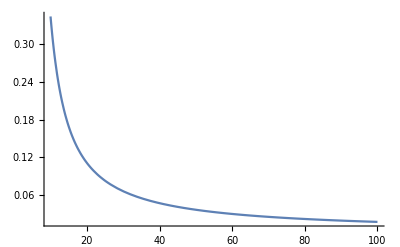

```mathematica
Plot[W,{x,10,100},PlotRange->All]
```

```mathematica
B=AsymptoticIntegrate[f4[t,x],{t,0,Pi/2-ArcTan[3]},{x,Infinity,3}](*Exact solution*)
```

(14170 ⅇ^(-x ArcTan[3]))/(27 x^4)+(1420 ⅇ^(-x ArcTan[3]))/(27 x^3)+(65 ⅇ^(-x ArcTan[3]))/(9 x^2)+(5 ⅇ^(-x ArcTan[3]))/(3 x)

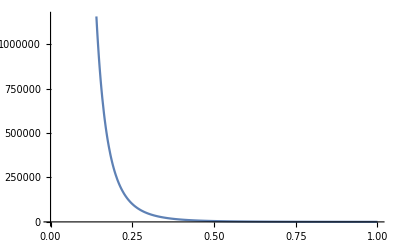

```mathematica
Plot[B,{x,0,1}]
```